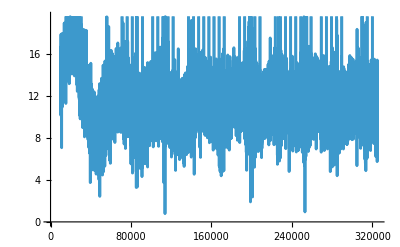

{{1584375/8,569171.,201232.},{1015625/4,242829.,85853.},{284375/2,126152.,44601.5}}

```mathematica
fs=65*10^4;

data=First@Import["/home/shaoyafan/develop/wavegen/raw_adc.txt","CSV"];

n=Length[data];
dataAC=data-Mean[data];
fft=Fourier[dataAC];
spectrum=Abs[fft];
freq=Range[0,n-1] fs/n;
half=Floor[n/2];
freqHalf=freq[[1;;half]];
specHalf=spectrum[[1;;half]];
band=Pick[Range[Length[freqHalf]],Thread[10000<=freqHalf<=500000]];
freqBand=freqHalf[[band]];
specBand=specHalf[[band]];
ListLinePlot[Transpose[{freqBand,specBand}]]
peaks=FindPeaks[specBand];
peaksSorted=Reverse@SortBy[peaks,Last];
components=Take[peaksSorted,UpTo[3]];
idx=components[[All,1]];
peakFreq=freqBand[[idx]];
peakAmplitude=2 specBand[[idx]] Sqrt[n];
vpp=2 peakAmplitude;
vrms=peakAmplitude/Sqrt[2];
result=Transpose[{peakFreq,vpp,vrms}]
```